```mathematica
NotebookInformation[]
```

{FileName→FrontEnd`FileName[{$RootDirectory,Users,ccarter,Projects_Local,dmse_git_hub,3029,development-material,Craigs_Development_Materials,Polymers},Random_Motion_Of_Polymer.nb,CharacterEncoding→UTF-8],FileModificationTime→3.85472×10^9,WindowTitle→Random_Motion_Of_Polymer.nb,MemoryModificationTime→3.85472×10^9,ModifiedInMemory→True,StorageSystem→Local,DocumentType→Notebook,MIMEType→application/vnd.wolfram.nb,StyleDefinitions→{FrontEndObject[LinkObject["i8kkj_shm", 3, 1]]4},ExpressionUUID→f221cdb3-a6df-4334-a826-7b43085048b4}

## Geometry in the frame where the blue particle moves along the x-axis:

### -Graphics-

### Equation for the position of the orange particle

```mathematica
{Δx2[s],Δy2[s]}={Δx1[s],0}  + {Cos[β[s]],Sin[β[s]]}
```

```mathematica
Cos[β[s] - Pi/2]
```

#### Let’s suppose that the rate of change of the angle β is proportional to the force projected in the radial direction of motion. ν is a “stickiness” coefficient. When ν=1, it will be rigid motion.

```mathematica
eq =D[β[s],s]== (1-ν) Sin[β[s]]
```

#### Let the initial angle be β_0

```mathematica
DSolve[  {eq,β[0]==β0},β[s],s]
```

```mathematica
β[s_,ν_,β0_]:= 2 ArcCot[ⅇ^(-s+s ν) Cot[β0/2]]
```

#### Use Rotation Transform to make the initial direction of the blue particle correspond with θ

```mathematica
DynamicModule[{p1,p2,p0},
Manipulate[
p1 = RotationTransform[θ][{s,0}];
p2 = RotationTransform[θ][{s,0} + AngleVector[β[s,ν,β0-θ]]];
Graphics[
{Blue,Circle[p1,1/2],
Orange,
Circle[p2,1/2]},
PlotRange->8{{-1,1},{-1,1}},Frame->True],
{s,0,5},
{θ,0, 2Pi},
{ν,0,1},
{β0,-Pi,Pi}
]
]
```

#### Example of 5 particles being dragged by particle #3

Note, the angles go like this: β21, β32,β33,β34,β45
The order of the angles changes.
The particles to the left of particle 3 have decreasing indices; the particles to the right have increasing indices.

```mathematica
DynamicModule[{d1,d2,d3,d4,d5, β33 =0},Manipulate[
Graphics[
d3 = s AngleVector[β[s,ν,β33]];
d4 = d3 + AngleVector[β[s,ν,β34-θ]];
d5 = d4 + AngleVector[β[s,ν,β45-θ]];
d2 = d3 + AngleVector[β[s,ν,β32-θ]];
d1 = d2 + AngleVector[β[s,ν,β21-θ]];

{Blue,
Circle[RotationMatrix[θ].d3,1/2],
Orange,
Circle[RotationMatrix[θ].d4,1/2],
Circle[RotationMatrix[θ].d5,1/2],
Circle[RotationMatrix[θ].d2,1/2],
Circle[RotationMatrix[θ].d1,1/2](*,
Line[{{0,0},1AngleVector[θ]}],
Blue,Orange,
Line[{RotationMatrix[θ].AngleVector[β[0,ν,β0-θ] ],RotationMatrix[θ].({s,0}+AngleVector[β[s,ν,β0-θ]])}]*)
,Black,
Text[1,RotationMatrix[θ].d1],
Text[2,RotationMatrix[θ].d2],
Text[3,RotationMatrix[θ].d3],
Text[4,RotationMatrix[θ].d4],
Text[5,RotationMatrix[θ].d5]


},
PlotRange->3{{-1,1},{-1,1}},Frame->True
],
{s,0,1},
{θ,0, 2Pi},
{ν,0,1},
{β45,-Pi,Pi},
{{β34,Pi/2},-Pi,Pi},
{{β32,-1},-Pi,Pi},
{{β21,-1},-Pi,Pi}
]
]
```

#### Illustration of the propagation of disturbance behavior of the subsequent points.

```mathematica
Clear[s,ν,θ];β33=0;
d3 = s AngleVector[β[s,ν,β33]];
d4 = d3 + AngleVector[β[s,ν,β34-θ]];
d5 = d4 + AngleVector[β[s,ν,β45-θ]];
d2 = d3 + AngleVector[β[s,ν,β32-θ]];
d1 = d2 + AngleVector[β[s,ν,β21-θ]];
RotationTransform[θ][{d1,d2,d3,d4,d5}]//FullSimplify//Grid
```

#### Note the recursive behavior of the terms as they propagate from the preceding link in the chain until they reach the particle that was set in motion (above, that particle was 3). Each term is the sum of its predecessor by sines and cosines of an “reduced” angle: We can precompute all of these reduced angles efficiently and then use a recursive definition to compute the displacements

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

For example:

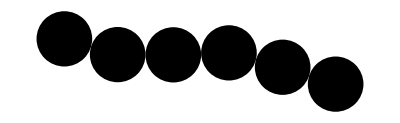

```mathematica
positions = AnglePath[RandomReal[{-.3,.3},5]];
Graphics[Disk[#,1/2]&/@positions]
```

```mathematica
Grid[precompute[positions,3,s,ν,θ],Frame->All]
```

Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (2.85259-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (2.85259-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (3.1373-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (3.1373-θ)]]]
Cos[θ] | Sin[θ]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (0.0357436-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (0.0357436-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.263076-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.263076-θ)]]]
Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.310738-θ)]]] | Sin[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-0.310738-θ)]]]

#### Here is the displacement function. It creates a recursive function each time it is called, and then uses recursion to compute each displacement, and memoizes (i.e., remembers) each computation.

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Which[
index> perturbedIndex,newPositions[index-1] + Δ[[index]],
True,newPositions[index+1] + Δ[[index]]];
newPositions/@Range[Length[Δ]]
]
```

Note: This function doesn’t check for collisions. We will fix that up later.

#### For example:

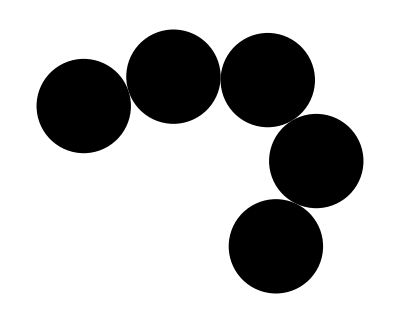

```mathematica
positions = AnglePath[RandomReal[{-1,1},4]];
Graphics[Disk[#,1/2]&/@positions]
```

```mathematica
displacements[2,positions,s,ν,θ]//Short
displacements[2,positions,.1,.1,Pi/3]
```

{{0.950369+s Cos[θ]+Cos[θ+2 ArcCot[ⅇ^(-s+s ν) Cot[1/2 (-«18»-θ)]]],«1»},«4»}

{{0.0696593,0.0319687},{1.00037,0.397726},{1.9935,0.280687},{2.43965,-0.614269},{2.00563,-1.51517}}

#### Visualization:

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions),
MapIndexed[Text[#2[[1]],#1]&,(positions)]}
```

```mathematica
DynamicModule[
{positions = AnglePath[RandomReal[{-1,1},8]]},
Manipulate[
If[reset,positions = AnglePath[RandomReal[{-1,1},8]];reset=False];
Graphics[
{ chainGraphic[displacements[i,positions,s,0,θ]],
{Red,PointSize[0.01],Point[positions[[i]]],Arrow[{positions[[i]],positions[[i]]+6 AngleVector[θ]}]}},
PlotRange->p{{-1,1},{-1,1}},Frame->True
],
{{s,0,Style["Displacement",14]},0,3},
{{θ,Pi/2,Style["Displacement Direction",14]},-Pi, Pi},
{{i,1,Style["Particle to Displace",14]},Range[Length[positions]]},
{{p,10,Style["Zoom",14]},2,20},
Delimiter,
{{reset,False,Style["Reset Initial Configuration",14]},{True,False}}
]
]
```

#### Using the visualization tool, you will see that the chain will occasionally “intersect” itself. This is because we have not included a collision detection algorithm yet. We will do that below. But, first let’s use our current model to illustrate how we will implement Brownian motion of a polymer.

### Random Motion

#### We will model the motion of an isolated particle by assuming that a temperature bath applies a random force to a randomly chosen atom in the chain.

```mathematica
positions = AnglePath[RandomReal[{-0.5,0.5},12]];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
Dynamic[currentGraphic]
```

```mathematica
With[{stiffness = 0, relativeTemperature = 0.2},
Do[
With[{whichParticle =RandomInteger[{1,Length[positions]}],
perturbation = RandomVariate[MaxwellDistribution[relativeTemperature]],
angle = RandomReal[2Pi]
},
(*positions =(Mean[positions]+#)&/@displacements[whichParticle,positions,perturbation,stiffness,angle];*)positions=displacements[whichParticle,positions,perturbation,stiffness,angle];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
];Pause[0.05],
{100}
]
]
```

### Collision Detection and Avoidance (seems to be working, but needs comments and good examle)

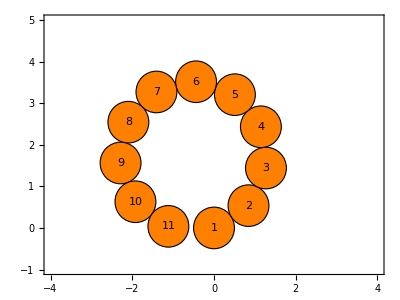

```mathematica
positions = AnglePath[ConstantArray[0.565,10]];
Graphics[chainGraphic[positions],PlotRange->{{-4,4},{-1,5}},Frame->True]
```

```mathematica
Manipulate[
Graphics[chainGraphic[displacements[11,positions,s,.1,0]],
PlotRange->{{-4,4},{-1,5}},Frame->True],
{s,0,1}
]
```

```mathematica
Union@Flatten[DistanceMatrix[displacements[11,positions,.126,.1,0]]+ IdentityMatrix[Length[positions]]]//N
```

{0.488437,1.,1.,1.,1.43435,1.44781,1.90105,1.90432,1.90517,1.91311,1.91434,1.92321,1.92434,1.93128,1.93203,2.2055,2.28766,2.30931,2.62024,2.62186,2.64333,2.64731,2.67954,2.68407,2.71442,2.71803,2.82552,2.83523,2.96807,2.9935,3.08771,3.11219,3.11858,3.1789,3.1802,3.19001,3.23468,3.24939,3.26255,3.27203,3.28591,3.29148,3.367,3.38128,3.3945,3.41818,3.5005,3.51777}

One approach would be to limit the magnitude of the perturbation distance so that no  collisions occur. For example:

```mathematica
Manipulate[
Union@Flatten[DistanceMatrix[displacements[11,positions,s,.1,0]]+ IdentityMatrix[Length[positions]]][[1;;10]],
{s,0,6}
]
```

This would be fairly easy to code.

Another approach would be to detect collisions in the recursive part in the displacements function.  If a collision is found, then that displacement is limited.

```mathematica
(*displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{displacement,betaList,Δ , computedPositions,collisionDistance },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = {displacement[perturbedIndex]};
Identity[{perturbedIndex,computedPositions}];
displacement[index_] := displacement[index]=
Which[
index> perturbedIndex,
With[{testPoint=displacement[index-1] + Δ[[index]]},
Echo[collisionDistance = Nearest[computedPositions->"Distance"][testPoint][[1]]];
Which[collisionDistance>= 1,Identity[ {index,index> perturbedIndex,AppendTo[computedPositions,testPoint]}];testPoint,
True, AppendTo[computedPositions,displacement[index-1]];displacement[index-1]]
],
True,
With[{testPoint=displacement[index+1] + Δ[[index]]},
Echo[collisionDistance = Nearest[computedPositions->"Distance"][testPoint][[1]]];
Which[collisionDistance>= 1,Identity[{index,index> perturbedIndex, AppendTo[computedPositions,testPoint]}];testPoint,
True, AppendTo[computedPositions,displacement[index+1]];displacement[index+1]]
]
];
displacement/@Range[Length[Δ]]
]*)
```

```mathematica
Clear[displacementsNew]
```

```mathematica
Options[displacementsNew]={"Return"->"Result"}
```

{Return→Result}

```mathematica
displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_,OptionsPattern[]]:= 
Block[{displacement,betaList,Δ , computedPositions,collisionDistance,results,overlap,minDistances },
(*Echo[s];*)
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = {displacement[perturbedIndex]};
(*#1*)
 displacement[index_] := displacement[index]=
Module[
{testPoint=displacement[index-Sign[index-perturbedIndex] ]+ Δ[[index]],
checkNearby ,collisions,notNearestNeighbors},
checkNearby =Nearest[computedPositions->All][testPoint,All];
(*#2*)
notNearestNeighbors=Select[Abs[#Index - perturbedIndex]> 1&][checkNearby];
(*Echo[notNearestNeighbors];*)
Which[
notNearestNeighbors =={},Sow[Nothing],
True,
collisions =Select[#Distance < 1&][notNearestNeighbors];
(*#3*)
If[collisions !={},Throw[collisions[[1,"Distance"]]]];
Sow[MinimalBy[#Distance&][notNearestNeighbors][[1,"Distance"]]]
];
(*#4*)
AppendTo[computedPositions,testPoint];
testPoint
];
(*#5*)
overlap = Catch[{results,minDistances}= Reap[displacement/@Range[Length[Δ]]]];
Which[
ListQ[overlap] && OptionValue["Return"]!="Distance",
results,
(*#6*)
ListQ[overlap] && OptionValue["Return"]=="Distance",
Min[minDistances],
NumericQ[overlap] && OptionValue["Return"]=="Distance",
Return[overlap],
(*#7*)
NumericQ[overlap] && overlap<1,
findNonTouchingDisplacement[perturbedIndex,positionList,{s,0},ν,θ]
]
]
```

Code Footnotes:
#1) This is a recursive function....
#2)  Because nearest neighbors are always distance=1, we don’t want to include....
#3)
#4)
#5)
#6)
#7)

```mathematica
findNonTouchingDisplacement[perturbedIndex_,positionList_,{sProducingDistanceLessThan1_,sProducingDistanceGreaterThan1_},ν_,θ_]:=
Module[
{greaterThan1 = sProducingDistanceGreaterThan1, lessThan1 = sProducingDistanceLessThan1,
search,
currentDistance,
tries = 1, maxtries = 50,lastGreater=0},
search = Mean[Echo@{lessThan1,greaterThan1}];
currentDistance = 0;
Echo[currentDistance];
(*#1*)
While[Abs[greaterThan1-lessThan1]> 0.0001 (*&& currentDistance<1*)&& ++tries < maxtries,
(*#2*)
currentDistance = displacementsNew[perturbedIndex,positionList,search,ν,θ,"Return"->"Distance"];
search = Mean[{lessThan1,greaterThan1}];
Which[
(*#3*)
currentDistance<1,lessThan1= search,
True,lastGreater=greaterThan1= search
];
Echo[{search,{lessThan1,greaterThan1},currentDistance<1,NumberForm[currentDistance,100]}];
];
If[tries>= maxtries,Print["Binary Search went weirdly wrong"]];
Echo[lastGreater,"last greater"];
(*#4*)
displacementsNew[perturbedIndex,positionList,lastGreater,ν,θ]
]
```

Code Footnotes:
#1)
#2)
#3)
#4)

```mathematica
test=displacementsNew[11,positions,.5,.1,0]
```

{0.5,0}

0

{0.25,{0.25,0},True,0.872141333467643}

{0.125,{0.125,0},True,0.872141333467643}

{0.0625,{0.0625,0},True,0.4934085277742543}

{0.03125,{0.03125,0},True,0.804801595007059}

{0.015625,{0.015625,0},True,0.960788210557326}

{0.0078125,{0.015625,0.0078125},False,1.}

{0.0117188,{0.015625,0.0117188},False,1.}

{0.0136719,{0.015625,0.0136719},False,1.}

{0.0146484,{0.015625,0.0146484},False,1.}

{0.0151367,{0.015625,0.0151367},False,1.}

{0.0153809,{0.015625,0.0153809},False,1.}

{0.0155029,{0.015625,0.0155029},False,1.}

{0.015564,{0.015625,0.015564},False,1.}

{0.0155945,{0.015625,0.0155945},False,1.}

{0.0156097,{0.015625,0.0156097},False,1.}

{0.0156174,{0.015625,0.0156174},False,1.}

{0.0156212,{0.015625,0.0156212},False,1.}

{0.0156231,{0.015625,0.0156231},False,1.}

{0.015624,{0.015625,0.015624},False,1.}

last greater  0.015624

{{-0.0624367,0.000525819},{0.786135,0.529606},{1.22423,1.42854},{1.11421,2.42247},{0.48674,3.2011},{-0.462181,3.51662},{-1.43062,3.26739},{-2.11015,2.53374},{-2.28778,1.54964},{-1.91159,0.623095},{-1.10058,0.038069}}